```mathematica
v[x_]:=a*V0/L/;x<=b/2
v[x_]:=-b*V0/L/;(x>b/2&&x<(b/2+a))
v[x_]:=a*V0/L/;(x>(b/2+a)&&x<(b+a))
```

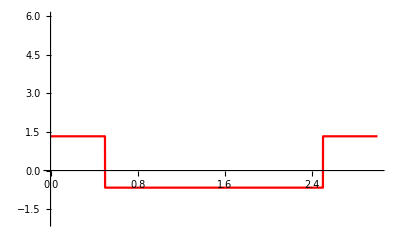

```mathematica
V0=2;b=1;a=2;L=a+b;
g1=Plot[v[x],{x,0,a+b},PlotRange->{-V0/2-1,V0/2+5},PlotStyle->Red]
```

```mathematica
precision=10;
integral1[n_]:=(a*V0/L)NIntegrate[Cos[n*2*Pi*x/(a+b)],{x,0,b/2},PrecisionGoal->precision];
integral2[n_]:=(-b*V0/L)NIntegrate[Cos[n*2*Pi*x/(a+b)],{x,b/2,b/2+a},PrecisionGoal->precision];
integral3[n_]:=(a*V0/L)NIntegrate[Cos[n*2*Pi*x/(a+b)],{x,b/2+a,b+a},PrecisionGoal->precision];
integral[n_]:=(1/L)(integral1[n]+integral2[n]+integral3[n]);
```

```mathematica
terminos=5;
tabla=Table[integral[i],{i,0,terminos}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.4999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained -1.38778×10^-17 and 4.94081×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.500000008967591079907500011341876778279968984719516811310313642}. NIntegrate obtained -2.7929×10^-16 and 9.78125×10^-14 for the integral and error estimates.

```mathematica
tabla
```

{0.,0.551329,0.275664,-1.07167×10^-16,-0.137832,-0.110266}

```mathematica
integral[1]
```

0.551329

```mathematica
serie=Sum[tabla[[i+1]]*Cos[i*2*Pi*x/(a+b)],{i,0,terminos}];
g2=Plot[2*serie,{x,0,(a+b)},PlotRange->{-V0/2-1,V0/2+5},PlotStyle->Black];
Show[g1,g2]
```

```mathematica
Plot[(2*serie-v[x])^2,{x,0,(a+b)},PlotRange->{0,2},PlotStyle->Black]
```

```mathematica
For[j=1,j≤10,j++,
terminos=j*10;
tabla=Table[integral[i],{i,0,terminos}];
serie=Sum[tabla[[i+1]]*Cos[i*2*Pi*x/(a+b)],{i,0,terminos}];
Print[terminos," términos =",NIntegrate[(2*serie-v[x])^2,{x,0,(a+b)}]]]
```

```mathematica
tamagno=21;
matrizA=Table[0.,{i,1,tamagno},{j,1,tamagno}];
For[i=1,i≤tamagno,i++,matrizA[[i,i]]=(i-(tamagno-1)/2-1)^2b^2/2];
For[i=1,i≤tamagno,i++,For[j=i+1,j≤tamagno,j++,matrizA[[i,j]]=integral[j-i]];
]
For[i=1,i≤tamagno,i++,For[j=1,j≤i-1,j++,matrizA[[i,j]]=matrizA[[j,i]]];
]
matrizA//MatrixForm
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.4999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained -1.38778×10^-17 and 4.94081×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.500000008967591079907500011341876778279968984719516811310313642}. NIntegrate obtained -2.7929×10^-16 and 9.78125×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.437492}. NIntegrate obtained -3.51282×10^-17 and 1.51947×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

(50 | 0.551329 | 0.275664 | -1.07167×10^-16 | -0.137832 | -0.110266 | -1.95638×10^-17 | 0.0787613 | 0.0689161 | -3.89349×10^-17 | -0.0551329 | -0.0501208 | -6.36065×10^-18 | 0.0424099 | 0.0393806 | 6.3221×10^-17 | -0.0344581 | -0.0324311 | 5.1078×10^-17 | 0.0290173 | 0.0275664
0.551329 | 81/2 | 0.551329 | 0.275664 | -1.07167×10^-16 | -0.137832 | -0.110266 | -1.95638×10^-17 | 0.0787613 | 0.0689161 | -3.89349×10^-17 | -0.0551329 | -0.0501208 | -6.36065×10^-18 | 0.0424099 | 0.0393806 | 6.3221×10^-17 | -0.0344581 | -0.0324311 | 5.1078×10^-17 | 0.0290173
0.275664 | 0.551329 | 32 | 0.551329 | 0.275664 | -1.07167×10^-16 | -0.137832 | -0.110266 | -1.95638×10^-17 | 0.0787613 | 0.0689161 | -3.89349×10^-17 | -0.0551329 | -0.0501208 | -6.36065×10^-18 | 0.0424099 | 0.0393806 | 6.3221×10^-17 | -0.0344581 | -0.0324311 | 5.1078×10^-17
-1.07167×10^-16 | 0.275664 | 0.551329 | 49/2 | 0.551329 | 0.275664 | -1.07167×10^-16 | -0.137832 | -0.110266 | -1.95638×10^-17 | 0.0787613 | 0.0689161 | -3.89349×10^-17 | -0.0551329 | -0.0501208 | -6.36065×10^-18 | 0.0424099 | 0.0393806 | 6.3221×10^-17 | -0.0344581 | -0.0324311
-0.137832 | -1.07167×10^-16 | 0.275664 | 0.551329 | 18 | 0.551329 | 0.275664 | -1.07167×10^-16 | -0.137832 | -0.110266 | -1.95638×10^-17 | 0.0787613 | 0.0689161 | -3.89349×10^-17 | -0.0551329 | -0.0501208 | -6.36065×10^-18 | 0.0424099 | 0.0393806 | 6.3221×10^-17 | -0.0344581
-0.110266 | -0.137832 | -1.07167×10^-16 | 0.275664 | 0.551329 | 25/2 | 0.551329 | 0.275664 | -1.07167×10^-16 | -0.137832 | -0.110266 | -1.95638×10^-17 | 0.0787613 | 0.0689161 | -3.89349×10^-17 | -0.0551329 | -0.0501208 | -6.36065×10^-18 | 0.0424099 | 0.0393806 | 6.3221×10^-17
-1.95638×10^-17 | -0.110266 | -0.137832 | -1.07167×10^-16 | 0.275664 | 0.551329 | 8 | 0.551329 | 0.275664 | -1.07167×10^-16 | -0.137832 | -0.110266 | -1.95638×10^-17 | 0.0787613 | 0.0689161 | -3.89349×10^-17 | -0.0551329 | -0.0501208 | -6.36065×10^-18 | 0.0424099 | 0.0393806
0.0787613 | -1.95638×10^-17 | -0.110266 | -0.137832 | -1.07167×10^-16 | 0.275664 | 0.551329 | 9/2 | 0.551329 | 0.275664 | -1.07167×10^-16 | -0.137832 | -0.110266 | -1.95638×10^-17 | 0.0787613 | 0.0689161 | -3.89349×10^-17 | -0.0551329 | -0.0501208 | -6.36065×10^-18 | 0.0424099
0.0689161 | 0.0787613 | -1.95638×10^-17 | -0.110266 | -0.137832 | -1.07167×10^-16 | 0.275664 | 0.551329 | 2 | 0.551329 | 0.275664 | -1.07167×10^-16 | -0.137832 | -0.110266 | -1.95638×10^-17 | 0.0787613 | 0.0689161 | -3.89349×10^-17 | -0.0551329 | -0.0501208 | -6.36065×10^-18
-3.89349×10^-17 | 0.0689161 | 0.0787613 | -1.95638×10^-17 | -0.110266 | -0.137832 | -1.07167×10^-16 | 0.275664 | 0.551329 | 1/2 | 0.551329 | 0.275664 | -1.07167×10^-16 | -0.137832 | -0.110266 | -1.95638×10^-17 | 0.0787613 | 0.0689161 | -3.89349×10^-17 | -0.0551329 | -0.0501208
-0.0551329 | -3.89349×10^-17 | 0.0689161 | 0.0787613 | -1.95638×10^-17 | -0.110266 | -0.137832 | -1.07167×10^-16 | 0.275664 | 0.551329 | 0 | 0.551329 | 0.275664 | -1.07167×10^-16 | -0.137832 | -0.110266 | -1.95638×10^-17 | 0.0787613 | 0.0689161 | -3.89349×10^-17 | -0.0551329
-0.0501208 | -0.0551329 | -3.89349×10^-17 | 0.0689161 | 0.0787613 | -1.95638×10^-17 | -0.110266 | -0.137832 | -1.07167×10^-16 | 0.275664 | 0.551329 | 1/2 | 0.551329 | 0.275664 | -1.07167×10^-16 | -0.137832 | -0.110266 | -1.95638×10^-17 | 0.0787613 | 0.0689161 | -3.89349×10^-17
-6.36065×10^-18 | -0.0501208 | -0.0551329 | -3.89349×10^-17 | 0.0689161 | 0.0787613 | -1.95638×10^-17 | -0.110266 | -0.137832 | -1.07167×10^-16 | 0.275664 | 0.551329 | 2 | 0.551329 | 0.275664 | -1.07167×10^-16 | -0.137832 | -0.110266 | -1.95638×10^-17 | 0.0787613 | 0.0689161
0.0424099 | -6.36065×10^-18 | -0.0501208 | -0.0551329 | -3.89349×10^-17 | 0.0689161 | 0.0787613 | -1.95638×10^-17 | -0.110266 | -0.137832 | -1.07167×10^-16 | 0.275664 | 0.551329 | 9/2 | 0.551329 | 0.275664 | -1.07167×10^-16 | -0.137832 | -0.110266 | -1.95638×10^-17 | 0.0787613
0.0393806 | 0.0424099 | -6.36065×10^-18 | -0.0501208 | -0.0551329 | -3.89349×10^-17 | 0.0689161 | 0.0787613 | -1.95638×10^-17 | -0.110266 | -0.137832 | -1.07167×10^-16 | 0.275664 | 0.551329 | 8 | 0.551329 | 0.275664 | -1.07167×10^-16 | -0.137832 | -0.110266 | -1.95638×10^-17
6.3221×10^-17 | 0.0393806 | 0.0424099 | -6.36065×10^-18 | -0.0501208 | -0.0551329 | -3.89349×10^-17 | 0.0689161 | 0.0787613 | -1.95638×10^-17 | -0.110266 | -0.137832 | -1.07167×10^-16 | 0.275664 | 0.551329 | 25/2 | 0.551329 | 0.275664 | -1.07167×10^-16 | -0.137832 | -0.110266
-0.0344581 | 6.3221×10^-17 | 0.0393806 | 0.0424099 | -6.36065×10^-18 | -0.0501208 | -0.0551329 | -3.89349×10^-17 | 0.0689161 | 0.0787613 | -1.95638×10^-17 | -0.110266 | -0.137832 | -1.07167×10^-16 | 0.275664 | 0.551329 | 18 | 0.551329 | 0.275664 | -1.07167×10^-16 | -0.137832
-0.0324311 | -0.0344581 | 6.3221×10^-17 | 0.0393806 | 0.0424099 | -6.36065×10^-18 | -0.0501208 | -0.0551329 | -3.89349×10^-17 | 0.0689161 | 0.0787613 | -1.95638×10^-17 | -0.110266 | -0.137832 | -1.07167×10^-16 | 0.275664 | 0.551329 | 49/2 | 0.551329 | 0.275664 | -1.07167×10^-16
5.1078×10^-17 | -0.0324311 | -0.0344581 | 6.3221×10^-17 | 0.0393806 | 0.0424099 | -6.36065×10^-18 | -0.0501208 | -0.0551329 | -3.89349×10^-17 | 0.0689161 | 0.0787613 | -1.95638×10^-17 | -0.110266 | -0.137832 | -1.07167×10^-16 | 0.275664 | 0.551329 | 32 | 0.551329 | 0.275664
0.0290173 | 5.1078×10^-17 | -0.0324311 | -0.0344581 | 6.3221×10^-17 | 0.0393806 | 0.0424099 | -6.36065×10^-18 | -0.0501208 | -0.0551329 | -3.89349×10^-17 | 0.0689161 | 0.0787613 | -1.95638×10^-17 | -0.110266 | -0.137832 | -1.07167×10^-16 | 0.275664 | 0.551329 | 81/2 | 0.551329
0.0275664 | 0.0290173 | 5.1078×10^-17 | -0.0324311 | -0.0344581 | 6.3221×10^-17 | 0.0393806 | 0.0424099 | -6.36065×10^-18 | -0.0501208 | -0.0551329 | -3.89349×10^-17 | 0.0689161 | 0.0787613 | -1.95638×10^-17 | -0.110266 | -0.137832 | -1.07167×10^-16 | 0.275664 | 0.551329 | 50)

```mathematica
Eigenvalues[matrizA]+b*V0/L
```

{8.86684,8.68969,5.31644,5.13675,2.88441,2.72278,1.47184,0.180232,0.731015}